```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model -> "./modelFiles/SMS-stop_FA/SMS-stop_FA"];
```

```mathematica
processHGG = { V[4],V[4]} -> {S[1]};
tops = CreateTopologies[1, 2->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
allDiags = InsertFields[tops, processHGG,InsertionLevel-> {Particles},ExcludeParticles->{F[12],V[1],V[2],V[3]}];
FR$ClassesTranslation
```

generic model {Lorentz} initialized

classes model {./modelFiles/SMS-stop_FA/SMS-stop_FA} initialized

in total: 2 Particles insertions

{A→V(1),Z→V(2),W→V(3),G→V(4),ghA→U(1),ghZ→U(2),ghWp→U(3),ghWm→U(4),ghG→U(5),ve→F(1),vm→F(2),vt→F(3),e→F(4),mu→F(5),ta→F(6),u→F(7),c→F(8),t→F(9),d→F(10),s→F(11),b→F(12),H→S(1),G0→S(2),GluonPropagator→S(3),chi→F(13),ST→S(4)}

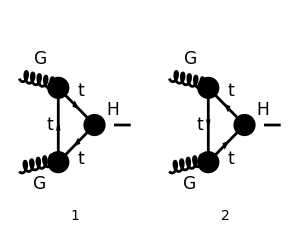

```mathematica
Paint[allDiags,ColumnsXRows->{2,1},PaintLevel->{Particles},ImageSize->{300,250},Numbering->Simple];
```

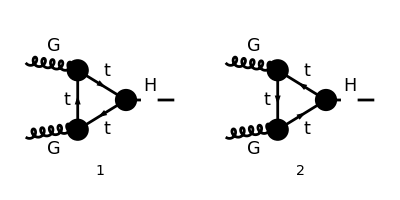

```mathematica
diags=DiagramExtract[allDiags,{1,2}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->False],IncomingMomenta->{p1,p2},OutgoingMomenta->{k},LoopMomenta->{q},List->False,TransversePolarizationVectors->{p1,p2},DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν,σ,ρ},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 2 Particles amplitudes

(ⅈ ε^μ(p1) ε^ν(p2) tr((γ·(-k+p2+q)+MT).(-(ⅈ yt)/(√2)).(MT+γ·(p2+q)).(-2 ⅈ √π √aS γ^ν T_Col4Col5^Glu2).(MT+γ·q).(-2 ⅈ √π √aS γ^μ T_Col5Col4^Glu1)))/((q^2-MT^2).((p2+q)^2-MT^2).((-k+p2+q)^2-MT^2))+(ⅈ ε^μ(p1) ε^ν(p2) tr((γ·(-k+p2+q)+MT).(-(ⅈ yt)/(√2)).(MT+γ·(p2+q)).(2 ⅈ √π √aS γ^ν T_Col5Col4^Glu2).(MT+γ·q).(2 ⅈ √π √aS γ^μ T_Col4Col5^Glu1)))/((q^2-MT^2).((p2+q)^2-MT^2).((-k+p2+q)^2-MT^2))

```mathematica
FCClearScalarProducts[];
ScalarProduct[k,k]=SMP["m_H"]^2;
ScalarProduct[p1,p1]=0;
ScalarProduct[p2,p2]=0;
ScalarProduct[p1,p2]=SMP["m_H"]^2/2;
```

```mathematica
amp[1]=SUNSimplify[FCTraceFactor[amp[0]]]
```

-(2 √2 π aS yt δ^Glu1Glu2 ε^μ(p1) ε^ν(p2) tr((MT-γ·(k-p2-q)).(MT+γ·(p2+q)).γ^ν.(MT+γ·q).γ^μ))/((q^2-MT^2).((p2+q)^2-MT^2).((k-p2-q)^2-MT^2))

PT = MTD[μ, ν] - FVD[p1, μ] FVD[p2, ν]/(s/2) ;(* Apply transverse polarization projector, since the gluons are transverse *) 
amp[2] = FullSimplify[DiracSimplify[Contract[PT amp[1]]]]

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[1]]]
```

-(8 √2 π aS MT yt δ^Glu1Glu2 ((ε(p1)·ε(p2)) (-k·p2+MT^2-q^2)+(k·ε(p2)) (p2·ε(p1))+2 (q·ε(p2)) (-(k·ε(p1))+p2·ε(p1)+2 (q·ε(p1)))))/((q^2-MT^2).((p2+q)^2-MT^2).((k-p2-q)^2-MT^2))

```mathematica
amp[3]=TID[amp[2],q,ToPaVe->True]//Simplify
```

1/((D-2) (k·p2)^2)8 ⅈ √2 π^3 aS MT yt δ^Glu1Glu2 (B_0(m_H^2,MT^2,MT^2) ((D-2) (ε(p1)·ε(p2)) (k·p2)^2-(k·p2) ((D-2) (k·ε(p2)) (p2·ε(p1))+MT m_H^2)+m_H^2 (k·ε(p2)) (p2·ε(p1)))+(k·p2) C_0(0,m_H^2,-2 (k·p2)+m_H^2,MT^2,MT^2,MT^2) ((D-2) (ε(p1)·ε(p2)) (k·p2)^2-(k·p2) ((D-2) (k·ε(p2)) (p2·ε(p1))+4 MT^3)+4 MT^2 (k·ε(p2)) (p2·ε(p1)))-(2 (k·p2)-m_H^2) (MT (k·p2)-(k·ε(p2)) (p2·ε(p1))) B_0(-2 (k·p2)+m_H^2,MT^2,MT^2))

```mathematica
amp[4]=ChangeDimension[amp[3],4]/.{D->4}//Simplify
```

1/(k̄·OverBar[p2])^2 4 ⅈ √2 π^3 aS MT yt δ^Glu1Glu2 (B_0(m_H^2,MT^2,MT^2) (2 (ε̄(p1)·ε̄(p2)) (k̄·OverBar[p2])^2-(k̄·OverBar[p2]) (2 (k̄·ε̄(p2)) (OverBar[p2]·ε̄(p1))+MT m_H^2)+m_H^2 (k̄·ε̄(p2)) (OverBar[p2]·ε̄(p1)))+2 (k̄·OverBar[p2]) ((ε̄(p1)·ε̄(p2)) (k̄·OverBar[p2])^2+2 MT^2 (k̄·ε̄(p2)) (OverBar[p2]·ε̄(p1))-(k̄·OverBar[p2]) ((k̄·ε̄(p2)) (OverBar[p2]·ε̄(p1))+2 MT^3)) C_0(0,m_H^2,-2 (k̄·OverBar[p2])+m_H^2,MT^2,MT^2,MT^2)-(2 (k̄·OverBar[p2])-m_H^2) (MT (k̄·OverBar[p2])-(k̄·ε̄(p2)) (OverBar[p2]·ε̄(p1))) B_0(-2 (k̄·OverBar[p2])+m_H^2,MT^2,MT^2))

```mathematica
amp[4]=FullSimplify[PaXEvaluate[amp[3],PaXC0Expand->True,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],Assumptions-> {s>0,MT>0}]
```

(ⅈ aS MT yt δ^Glu1Glu2 ((s-2 MT^2) log^2((√(s (s-4 MT^2))+2 MT^2-s)/(2 MT^2))+2 √(s (s-4 MT^2)) log((√(s (s-4 MT^2))+2 MT^2-s)/(2 MT^2))+2 s))/(√2 π s)

```mathematica
Quit[];
```

```mathematica
Needs["X`"]
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
amp[0]=PVC[0,1,0,mc^2, 2 mc^2 + s,mc^2,m,M,M]
```

C_1(mc^2,2 mc^2+s,mc^2;m,M,M)

```mathematica
LoopRefine[amp[0],Part-> UVDivergent]
```

0

```mathematica
amp[1]=LoopRefine[amp[0]]//DiscExpand//FullSimplify
```

-(2 (m^2-M^2+mc^2) C_0(mc^2,mc^2,2 mc^2+s;M,m,M)-(2 λ^(1/2)(m^2,M^2,mc^2) log((λ^(1/2)(m^2,M^2,mc^2)+m^2+M^2-mc^2)/(2 m M)))/mc^2+((m^2-M^2+mc^2) log(m^2/M^2))/mc^2+(2 √((2 mc^2+s) (-4 M^2+2 mc^2+s)) log((√((2 mc^2+s) (-4 M^2+2 mc^2+s))+2 M^2-2 mc^2-s)/(2 M^2)))/(2 mc^2+s))/(2 (2 mc^2-s))

```mathematica
amp[2]=FullSimplify[amp[1]/.{s-> (Subscript[a, s] M)^2,mc-> Subscript[a, c] M,m-> Subscript[a, t] M},Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0}]
```

-1/(M^2 (2 (a^c)^2-(a^s)^2))((((a^c)^2+(a^t)^2-1) (M^2 (a^c)^2 C_0(M^2 (a^c)^2,M^2 (a^c)^2,M^2 (2 (a^c)^2+(a^s)^2);M,M a^t,M)+log(a^t)))/((a^c)^2)+(λ^(1/2)(M^2,M^2 (a^c)^2,M^2 (a^t)^2) (-log(λ^(1/2)(M^2,M^2 (a^c)^2,M^2 (a^t)^2)+M^2 (-(a^c)^2+(a^t)^2+1))+log(a^t)+2 log(M)+log(2)))/(M^2 (a^c)^2)+√(1-4/(2 (a^c)^2+(a^s)^2)) log(1/2 (√((2 (a^c)^2+(a^s)^2-4) (2 (a^c)^2+(a^s)^2))-2 (a^c)^2-(a^s)^2+2)))

```mathematica
amp0=FullSimplify[Normal[LoopRefineSeries[amp[2],{Subscript[a, s],0,1},{Subscript[a, t],0,1},{Subscript[a, c],0,1}]],Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0}]
```

7/(12 M^2)

```mathematica
amp1=FullSimplify[Normal[LoopRefineSeries[amp[2],{Subscript[a, s],0,1},{Subscript[a, t],0,1}]],Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0,Subscript[a, c]<1}]
```

-(M^2 ((a^c)^2-1) (a^c)^2 C_0(M^2 (a^c)^2,M^2 (a^c)^2,2 M^2 (a^c)^2;M,M a^t,M)+√((a^c)^2-2) a^c log(a^c (√((a^c)^2-2)-a^c)+1)+((a^c)^2-1) log(1-(a^c)^2))/(2 M^2 (a^c)^4)